# Project 1 - IX1501

## A project by William Lewin & Elias Chahine

wlewin@kth.se & echahine@kth.se

## Summary

In the discrete math course you learned how to do a census by computing all possibilities and use the classical definition of probability. In the following problems you are expected to use convolution.
-Graphics-
At a dice game you throw five dice in the form of the Platonic solids. The dice are numbered with integers 1,2,…,n where n is the number of sides. The tetrahedron has its result number (1-4) written at the vertex pointing up. All other bodies have the result number on the side facing up. 

At a fun-fair stall you can win a giant Teddy bear if you participate in the mentioned dice game. You invest €2 and then throw the five dice. If the sum S satisfies S≤10 or S≥45 you will win the Teddy.

Determine the exact probability function of the sum.

The exact probability function of the sum is calculated using convolution on the separate probability function of each die.

Determine the exact probability of winning the Teddy prize. Also give a floating point answer.

The exact probability of winning teddy prize was calculated by summarizing each discrete value which were a failure requirement. These were then subtracted from the total probability, resulting in the probability of winning a Teddy prize on an individual try.

Determine the expected investment to win a Teddy

The expected investment to win a Teddy was calculated using the average number of tries required to win a Teddy, multiplied with the cost of a single try.

What’s the probability of winning (at least one) Teddy if you play twenty times?

The probability of winning at least one Teddy was calculated by calculating the inverse of not winning any Teddy prize from twenty tries.

## Mathematic formulas & equations

### Determine the exact probability function of the sum.

Each die is fair in this case, giving an equal chance of landing on each face. 
P(X = k) is then 1/k.

### Determine the exact probability of winning the Teddy prize. Also give a floating point answer.

### Determine the expected investment to win a Teddy.

### What’s the probability of winning (at least one) Teddy if you play twenty times?

## Discussion

## Code

```mathematica
ClearAll["`*"]
```

```mathematica
(*Question number one*)
(*Probability function of each die*)
pyramidfX[k_]=Piecewise[{{1/4,1≤k≤4}}];
cubefX[k_]=Piecewise[{{1/6,1≤k≤6}}];
octafX[k_]:=Piecewise[{{1/8,1≤k≤8}}];
dodefX[k_]:=Piecewise[{{1/12,1≤k≤12}}];
icofX[k_]:=Piecewise[{{1/20,1≤k≤20}}];

(*Convolve each probability function*)
convolutePyramidCube[k_]=DiscreteConvolve[pyramidfX[x],cubefX[x],x,k];
convolutePCOctagon[k_]=DiscreteConvolve[convolutePyramidCube[x],octafX[x],x,k];
convolutePCODodecahedron[k_]= DiscreteConvolve[convolutePCOctagon[x],dodefX[x],x,k];
convolutePCODIcosahedron[k_]=DiscreteConvolve[convolutePCODodecahedron[x],icofX[x],x,k];

(*Plot convolved function*)
DiscretePlot[convolutePCODIcosahedron[x],{x,0,50}];
(*Probability function of sum*)
convolutePCODIcosahedron[x];
```

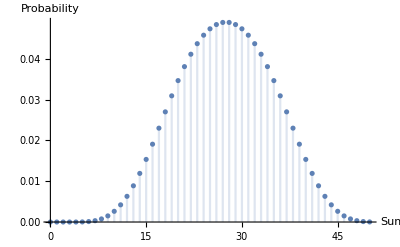

```mathematica
Show[%870,AxesLabel->{HoldForm[Sum],HoldForm[Probability]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
(*Question number two*)
(*Probability of Failure*)
probFail :=Sum[convolutePCODIcosahedron[x],{x,11,44}];
(*Probability of Failure Plot*)
probFailPlot:=DiscretePlot[convolutePCODIcosahedron[x],{x,11,44}];
(*Probability of Sucess Plot*)
probSucessPlot10:=DiscretePlot[convolutePCODIcosahedron[x],{x,5,10}];
probSucessPlot45:=DiscretePlot[convolutePCODIcosahedron[x],{x,45,50}];
(*Probability of Sucess*)
probSucess:= 1-probFail;
```

```mathematica
Print["Probability of Failure = ",probFail , " = ", N[probFail]]
Print["Probability of Sucess = ",probSucess," = ", N[probSucess]]
```

Probability of Failure = 3799/3840 = 0.989323

Probability of Sucess = 41/3840 = 0.0106771

```mathematica
(*Question number three*)
tryPrice := 2;
(*Expected number of trials until sucess*)
expectedTrials:= 1/probSucess; 
expectedInvestment := expectedTrials*tryPrice;
Print["Expected investment = ",expectedInvestment, " = ", Round[expectedInvestment]]
```

Expected investment = 7680/41 = 187

```mathematica
(*Question number four*)
tries:= 20;
wins := 0;
(*Binomial Distribution*)
probNotWinning= Binomial[tries,wins]*(probSucess^(wins))*((1-probSucess)^(tries-wins));
probWinning = 1-probNotWinning;
Print["Probability of winning atleast once = ", probWinning, " = " , N[probWinning]]
```

Probability of winning atleast once = 93896720713692929068924170210101909985514754789674511350420879336475999/485986815555701405566977235358756074107883642001817600000000000000000000 = 0.193208